# Kinetics Data Analysis

## v1

Alexander D. Schwab & Jefferson E. Bates

Department of Chemistry and Fermentation Sciences

Fall 2023

## Helper Functions

This data was measured by Dr. Schwab & Bates and has the following order: Mix #1, Mix #2, Mix #3, Mix #4, Mix #1 10C, Mix #1 40C. 
The reference concentrations are the expected concentrations for Mixtures 1-4.

```mathematica
Clear[importAndTransformData]
(***
Purpose : take input time,absorbance data and output pairs according to each trial, headers are also an outout. 
Input : filepath string to the data file
***)
importAndTransformData[filename_]:=Module[{listOfLists,output,headers,xValues,yValues,pairedList},
listOfLists=Import[filename,"CSV"];
headers=listOfLists[[1,2;;]];
xValues=listOfLists[[2;;,1]];
(*Start from the specified row for x values*)output={};
Do[yValues=listOfLists[[2;;,i]];(*Start from the specified row for y values*)pairedList=Transpose[{xValues,yValues}];
AppendTo[output,pairedList],{i,2,Length[listOfLists[[1]]]}];
Return[{headers,output}]
]
```

```mathematica
ratelist={};
```

## Process your experimental data - Example

Follow along with your instructor as you work through one trial of data together. Then you will be asked to process the remaining trials.

#### Import & Plot your experimental data - Exercise

To import your data, we will use a custom import function to help us format the data into {time,abs} pairs for each mixture. Update the filename variable below with the File Path to your experimental data. This should be a csv file from the instrument!

```mathematica
filename="/Users/batesje/Downloads/kinetics - sample data - Spring 2024.csv";
```

Now that you have your file ready, we can import and plot the data. Two lists are generated in the cell below; experimentheaders contains the text headers describing your columns, and experimentdata contains the {time,abs} data pairs for each mixture.

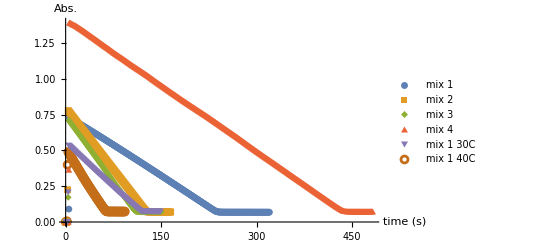

Absorbance_vs_time.png

```mathematica
{experimentheaders,experimentdata}=importAndTransformData[filename];
ListPlot[experimentdata,PlotLegends->Map[Style[#,14]&,experimentheaders],PlotMarkers->{Automatic,Small},AxesLabel->{Style["time (s)",14],Style["Abs.",14]},PlotRange->All]
Export["Absorbance_vs_time.png",%,"PNG"]
```

### Process data for Mix #1 - Example

Before we can begin processing the data, let’s set a variable that will help us select the appropriate data set.

```mathematica
datasettofit=1;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

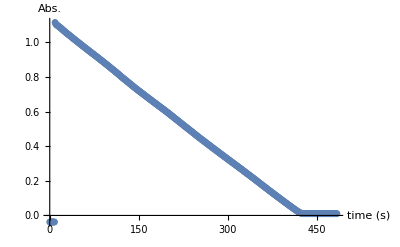

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=20;
endtime=225;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

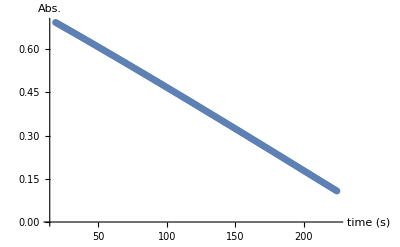

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[0.751993-0.00286252 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.001;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 1 rate : 3.80657×10^-6

## Process your experimental data - Exercise

Now that you have seen the process applied to a single data trial, you can apply the same steps to extract the rates of the other mixtures. Using copy & paste, take the needed code above under Process data for Mix #1 and make the appropriate changes to process the remaining mixtures in your data set. To do this you will need to:
    1. Update datasettofit to the correct integer
    2. Determine the appropriate start and end time for your selected trial
    3. Update the initial concentration to correspond to that for your selected trial
    4. Execute the cells to obtain your rate

### Process data for Mix #2 - Exercise

Work in this section for Mixture #2

```mathematica
datasettofit=2;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

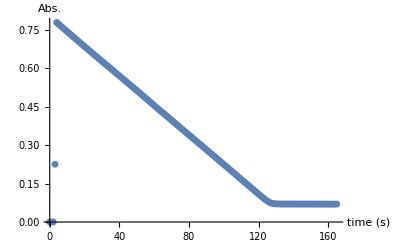

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=20;
endtime=115;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

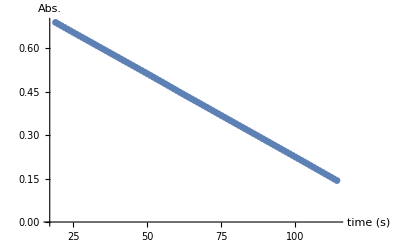

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[0.799708-0.00575254 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.001;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 2 rate : 7.19329×10^-6

### Process data for Mix #3 - Exercise

Work in this section for Mixture #3

```mathematica
datasettofit=3;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

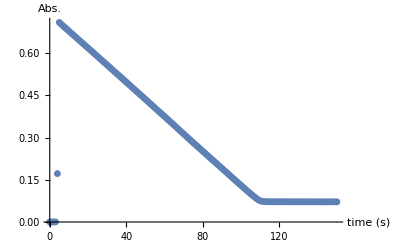

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=15;
endtime=90;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

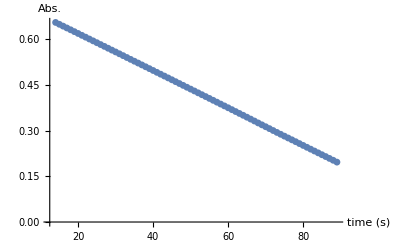

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[0.741968-0.00612597 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.001;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 3 rate : 8.25639×10^-6

### Process data for Mix #4 - Exercise

Work in this section for Mixture #4

```mathematica
datasettofit=4;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

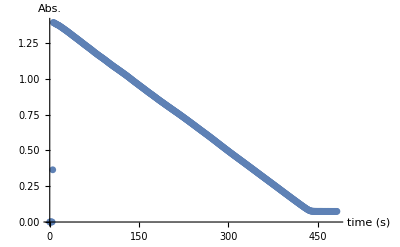

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=15;
endtime=410;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

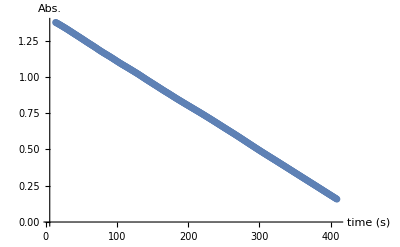

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[1.41874-0.00307956 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.002;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 4 rate : 4.34128×10^-6

### Process data for for Mix #1 @ 2nd Temperature - Exercise

Work in this section for Mixture #1 @ 2nd Temperature

Before we can begin processing the data, let’s set a variable that will help us select the appropriate data set.

```mathematica
datasettofit=5;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

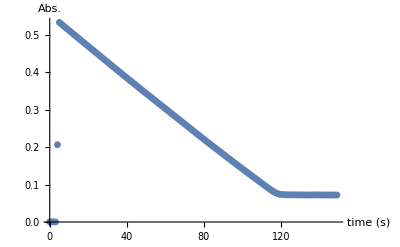

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=15;
endtime=115;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

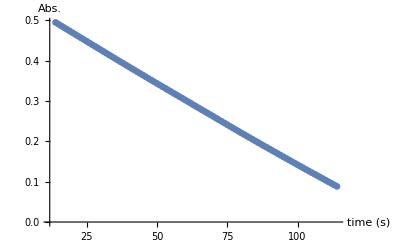

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[0.548922-0.00407621 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.001;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 1 30C rate : 7.42584×10^-6

### Process data for for Mix #1 @ 3rd Temperature - Exercise

Work in this section for Mixture #1 @ 3rd Temperature

### Process data for for Mix #1 @ 2nd Temperature - Exercise

Work in this section for Mixture #1 @ 2nd Temperature

Before we can begin processing the data, let’s set a variable that will help us select the appropriate data set.

```mathematica
datasettofit=6;
```

#### Plot the data in order to find a linear region - Example

It is expected that the data collected in the first 10 to 20 seconds of the experiment is unreliable as the solutions are being mixed and placed in the instrument, and that data collection may have taken place for a time period after which the reaction has completed and the absorbance is nearly 0. We need to trim both of these portions of data to allow for a proper linear fit of the absorbance vs time data. Using your interactive plot, or by right-clicking on the graph above and choosing “get coordinates”, hover over the data and determine an appropriate start time and ending time for this experimental data.

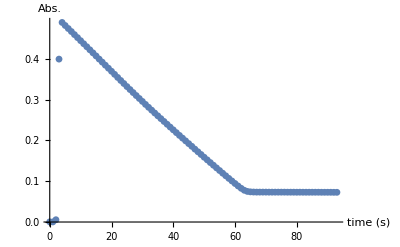

```mathematica
ListPlot[experimentdata[[datasettofit]],PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Specify your start and end time for the reaction and extract data to fit - Exercise

After you have investigated the plot above, enter your chosen values for the start and ending time of the reaction. These values should be positive integers!

```mathematica
starttime=10;
endtime=60;
```

Using the start and end times you specified above, we can extract the data to fit and re-plot it to make sure that the data is appropriately linear. Execute the code below to ensure you’ve chosen a reasonable value for the start and end time of the reaction. If you need to refine your values execute this set of Code Blocks again after updating your values. By executing the code below you create the variable datatofit which will be used below.

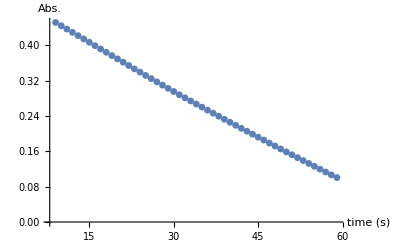

```mathematica
datatofit=experimentdata[[datasettofit]][[starttime;;endtime]];
ListPlot[datatofit,PlotLegends->Automatic,PlotMarkers->{Automatic,Small},AxesLabel->{"time (s)","Abs."},PlotRange->All]
```

#### Perform a linear fit of the data - Example

With our datatofit in hand, we can perform a linear fit of the data using NonlinearModelFit, like we have done in another experiment. We will use the model function: 
f(t) = m * t + b
Once we have the linear fit, the intercept corresponds to the extrapolated absorbance at the start of the reaction (time = 0 s), A_0, and the slope is related to the rate as described in the lab manual. The output of this cell is linearfit which we will use below.

```mathematica
linearfit=NonlinearModelFit[datatofit,m*t+b,{b,m},t]
```

FittedModel[0.510125-0.00704002 t]

#### Multiply the slope by [I_2]_0/A_0 to obtain the rate of the reaction - Example

Now that you have obtained the slope of your absorbance data, you can use this to determine the rate of the reaction according to the equations in the lab manual. 
rate = -d[I_2]/dt=-([I_2]_0)/A_0 dA_464/dt= -([I_2]_0)/A_0*slope

In order to obtain the rate, we need to multiply the Abs by the initial concentration. Since the absorbance is 1 at t = 0 when the reaction started, the concentration should be equal to the initial concentration of iodine, [I_2]_0. Specify the concentration of your mixture below in the initialconcentration variable. Mixtures 1-3 have [I_2]_0 = 0.001 and Mixture 4 has [I_2]_0 = 0.002.
We also store the rate in the variable ratelist for use later.

```mathematica
initialconcentration=0.001;
```

```mathematica
{A0,slope}={b,m}/.linearfit["BestFitParameters"];
{A0Error,slopeError}=linearfit["ParameterErrors"];
ratevalue=-initialconcentration/A0*slope;
AppendTo[ratelist,ratevalue];
Print[Framed[experimentheaders[[datasettofit]] <> " rate : " <>ToString[ratevalue,TraditionalForm],FrameStyle->Red]
]
```

mix 1 40C rate : 0.0000138006

### Table of Rate Data - Example

Now that we have calculated the rates, they have been stored in ratelist and we can make a nice table to summarize:

```mathematica
TableForm[Prepend[Transpose[{experimentheaders,ratelist}],{"","Rate"}]]
```

| Rate
mix 1 | 3.80657×10^-6
mix 2 | 7.19329×10^-6
mix 3 | 8.25639×10^-6
mix 4 | 4.34128×10^-6
mix 1 30C | 7.42584×10^-6
mix 1 40C | 0.0000138006

## Determine Orders of Reaction in [Acetone], [HCl], and [I_2] - Exercise

Once you have determined your rates for each mixture, you are able to determine the order of the reaction in each reactant by comparing trials that differ in the concentration of only a single species. This is due to the form of the rate law:
		Rate = k (([CH_3 COCH_3]^m [HCl])^n [I_2])^p
where m, n, and p are the orders of the reaction with respect to each reactant. Follow the instructions below to process your data and determine the orders of the reaction with respect to each reactant.

### Determining m - Acetone Exponent - Trials 1 & 2 - Exercise

Using your data from Trials 1 & 2 you are able to determine the order of the reaction with respect to acetone since these two trials only differ in their concentrations of acetone. By forming a ratio of the rates of these two trials we have: 
	Rate_2/Rate_1=((((k [Acetone_2])^m [HCl])^n[I_2])^p)/((((k [Acetone_1])^m [HCl])^n[I_2])^p) =  ([Acetone_2]/[Acetone_1])^m
which  we can then take a natural logarithm of in order to isolate the exponent m: 
	m = (Log(Rate_2/Rate_1))/(Log([Acetone_2]/[Acetone_1]))

Using the rates you calculated above, and the concentrations of Acetone from your experimental Mixtures #1 & #2, calculate the value of the exponent m. The final value for the rate law must be an integer, so you will need to round this value to the nearest whole number. Note: you can refer to the rates inside ratelist if you know which number corresponds to which trial. for instance the sample data above has ratelist[[1]] = 2.36475 x10^-6.

```mathematica
mvalue = Log[ratelist[[2]]/ratelist[[1]]]/Log[2]
```

0.91816

### Determining n - HCl Exponent - Trials 1 & 3 - Exercise

Using your data from Trials 1 & 3 you are able to determine the order of the reaction with respect to the acid (HCl) since these two trials only differ in their concentrations of acid. By forming a ratio of the rates of these two trials we have: 
	Rate_3/Rate_1=((((k [Acetone])^m [HCl_3])^n[I_2])^p)/((((k [Acetone])^m [HCl_1])^n[I_2])^p) =  ([HCl_3]/[HCl_1])^n
which  we can then take a (natural) logarithm of in order to isolate the exponent n: 
	n = (Log(Rate_3/Rate_1))/(Log([HCl_3]/[HCl_1]))

Using the rates you calculated above, and the concentrations of acid from your experimental Mixtures #1 & #3, calculate the value of the exponent n. The final value for the rate law must be an integer, so you will need to round this value to the nearest whole number.

```mathematica
nvalue = Log[ratelist[[3]]/ratelist[[1]]]/Log[2]
```

1.11702

### Determining p - I_2 Exponent - Trials 1 & 4 - Exercise

Using your data from Trials 1 & 4 you are able to determine the order of the reaction with respect to iodine since these two trials only differ in their concentrations of iodine. By forming a ratio of the rates of these two trials we have: 
	Rate_3/Rate_1=((((k [Acetone])^m [HCl])^n[I2_4])^p)/((((k [Acetone])^m [HCl])^n[I2_1])^p) =  ([I2_4]/[I2_1])^p
which  we can then take a (natural) logarithm of in order to isolate the exponent p: 
	p = (Log(Rate_4/Rate_1))/(Log([I2_4]/[I2_1]))

Using the rates you calculated above, and the concentrations of iodine from your experimental Mixtures #1 & #4, calculate the value of the exponent p. The final value for the rate law must be an integer, so you will need to round this value to the nearest whole number.

```mathematica
pvalue=Log[ratelist[[4]]/ratelist[[1]]]/Log[2]
```

0.189628

## Determine the Rate Constants - Exercise

Once you have determined the orders for each of the reactants, you can finally calculate the rate constant for each of your trials.  Modify the rate law below to reflect the actual values of m, n, and p. You will use this to finish your calculations.
		Rate = k (([CH_3 COCH_3]^m [HCl])^n [I_2])^p
Once you have your rate law finalized, solve the expression for the unknown rate constant, k! Use this equation to calculate the rate constants for each of your trials. Note: you can reference the rates from ratelist using list reference if you know which trial you’re interested in. For Mixture #1, ratelist[[1]], Mixture #2, ratelist[[2]], and so on in increasing numerical order.

## Calculate the Activation Energy through nonlinear fitting - Exercise

The rate constant, k, is only constant for a given temperature, otherwise this “constant” is really a function of temperature. This temperature dependence is difficult to describe from first principles, but tends to follow an Arrhenius behavior for many chemical reactions. As a result, the temperature dependence of the rate constant is:
	k(T) = A e^(-E_a/(RT))
where A is a pre-exponential factor (units depend on the reaction, can be temperature dependent), E_a is the activation energy (in J/mol), R is the universal gas constant (8.314 J/(mol K)), and T is the temperature (in Kelvin) at which the reaction takes place. 

Since you measured the rate constant of Mixture #1 at three temperatures, we can perform a nonlinear fit of the data to this functional form in order to extract the activation energy.

### Input temperature data in order to fit the Arrhenius equation - Exercise

In order to perform a fit of the data, we need to get the data into the proper format. The NonlinearModelFit function we have used previously requires {x,y} data pairs and in this case our data pairs are {T(in Kelvin), k}. Therefore we need to create a list of data points for our three temperatures of Mixture #1 in order to fit the Arrhenius equation.

Create a list with the three data points of your temperature data named temperaturedata.  This object should have the form: { {T_1,k_1},{T_2,k_2},{T_3,k_3} }. You can also plot this data with ListPlot[ ] or look at it in TableForm[ ] to ensure the values are correctly paired.

```mathematica
temperaturedata={{10+273.15,2.37955763*10^-5},{30+273.15,4.63826148*10^-5},{40+273.15,8.60747500*10^-5}}
```

{{283.15,0.0000237956},{303.15,0.0000463826},{313.15,0.0000860748}}

### Perform a nonlinear fit of the temperature data to get the activation energy - Example

Now that you have temperaturedata, we are ready to perform a nonlinear fit and extract the activation energy. Execute the cell below in order to create the Arrheniusfit object and extract the fit constants, Aexp & Ea. Instead of just using T, we will use Trx as the temperature of the reaction (in Kelvin).

```mathematica
Arrheniuseq=Aexp*Exp[-Ea/(8.314*Trx)];
Arrheniusfit=  NonlinearModelFit[temperaturedata,Arrheniuseq,{{Aexp,10^6},Ea},Trx,MaxIterations->2000]
{AValue,EaValue}={Aexp,Ea}/.Arrheniusfit["BestFitParameters"]
{AErr,EaError}=Arrheniusfit["ParameterErrors"];
Print[Framed["The R^2 for this fit is : " <> ToString[Arrheniusfit["RSquared"]],FrameStyle->Red]]
Print[Framed["The activation energy and its uncertainty , E_a ± ΔE_a = " <> ToString[EaValue]<> " ± " <> ToString[EaError],FrameStyle->Red]]
Print[Framed["The pre-exp factor and its uncertainty , A ± ΔA = " <> ToString[AValue,TraditionalForm]<> " ± " <> ToString[AErr,TraditionalForm],FrameStyle->Red]]
```

FittedModel[119.887 ⅇ^(-4439.54/Trx)]

{119.887,36910.4}

The R^2 for this fit is : 0.993203

The activation energy and its uncertainty , E_a ± ΔE_a = 36910.4 ± 9419.55

The pre-exp factor and its uncertainty , A ± ΔA = 119.887 ± 439.338

We can also plot our fit of the data and Export[ ] this to a file for later reference.

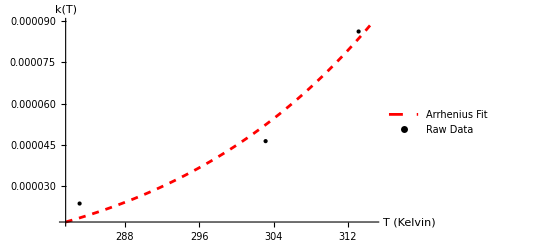

Arrhenius_plot.png

```mathematica
xmin=Min[temperaturedata[[All,1]]];
xmax=Max[temperaturedata[[All,1]]];
xrange=xmax-xmin;
xminplot = xmin-0.05*xrange;
xmaxplot=xmax+0.05*xrange;
Show[Plot[Arrheniusfit[x],{x,xminplot,xmaxplot},PlotRange->All,PlotStyle->{Red,Dashed,Thick},PlotLegends->{Style["Arrhenius Fit",14]}],ListPlot[temperaturedata,PlotStyle->{Black,PointSize[Large]},PlotLegends->{"Raw Data"}],AxesLabel->{HoldForm[Style["T (Kelvin)",14]],HoldForm[Style["k(T)",14]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
Export["Arrhenius_plot.png",%,"PNG"]
```